# FivePointConic

Find a conic equation that passes through five given points

## Definition

```mathematica
FivePointConic[pts_]/;MatrixQ[pts]&&Dimensions[pts]==={5,2}:=FivePointConic[pts,{x,y}];FivePointConic[pts_,{xx_,yy_}]/;MatrixQ[pts]&&Dimensions[pts]==={5,2}:=Times@@Apply[Power,DeleteCases[FactorList[Det[PadLeft[Apply[Function[{x,y},{x,y,x^2,x y,y^2}],Append[pts,{xx,yy}],{1}],{6,6},1]]],{_?NumericQ,_}],{1}]
```

## Documentation

### Usage

FivePointConic[pts,{x,y}]

returns the implicit Cartesian equation in the variables x and y of the conic section that goes through the points pts.

FivePointConic[pts]

uses the formal variables x and y.

### Details & Options

For random, uniformly-distributed points in a rectangle, the probability of a hyperbola is 95/144 and the probability of an ellipse is 49/144.

## Examples

### Basic Examples

Find a conic section through five points:

```mathematica
p5={{1,4},{4,2},{2,8},{8,5},{5,7}};
conic=FivePointConic[p5,{x,y}]
```

1638-333 x+19 x^2-531 y+36 x y+41 y^2

Show the conic and points:

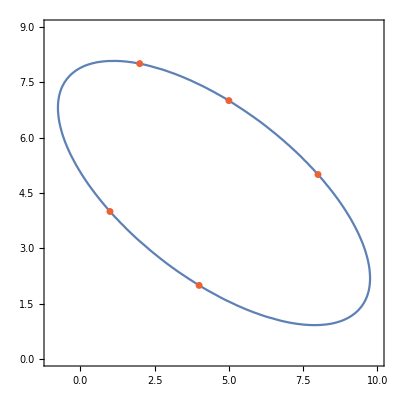

```mathematica
ContourPlot[conic==0,{x,-1,10},{y,0,9},Epilog->{,Point[p5]}]
```

### Scope

Use formal variables:

```mathematica
FivePointConic[{{1,4},{4,2},{2,8},{8,5},{5,7}}]
```

1638-333 x+19 x^2-531 y+36 x y+41 y^2

The results of a five point conic are usually a hyperbola:

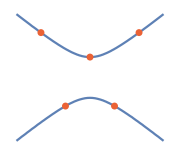
-Graphics-2 x^2-5 y-3 y^2

```mathematica
points={{-2,1},{-1,-2},{1,-2},{2,1},{0,0}};
conic=FivePointConic[points,{x,y}];
curve=ContourPlot[conic==0,{x,-3,3},{y,-4,4}][[1]];
Labeled[Graphics[{curve,{,Point[points]}}, ImageSize-> Small],conic]
```

A random five point conic is also frequently an ellipse:

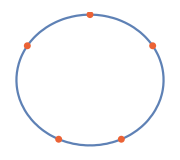
-Graphics--22+4 x^2+y+5 y^2

```mathematica
points={{-2,1},{-1,-2},{1,-2},{2,1},{0,2}};
conic=FivePointConic[points,{x,y}];
curve=ContourPlot[conic==0,{x,-3,3},{y,-4,4}][[1]];
Labeled[Graphics[{curve,{,Point[points]}}, ImageSize-> Small],conic]
```

A circle can also be the result of a five point conic:

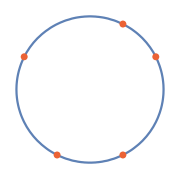
-Graphics--5+x^2+y^2

```mathematica
points={{-2,1},{-1,-2},{1,-2},{2,1},{1,2}};
conic=FivePointConic[points,{x,y}];
curve=ContourPlot[conic==0,{x,-3,3},{y,-4,4}][[1]];
Labeled[Graphics[{curve,{,Point[points]}}, ImageSize-> Small],conic]
```

A parabola may also appear:

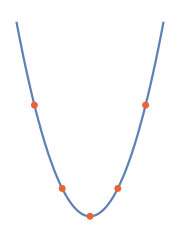
-Graphics--3+x^2-y

```mathematica
points={{-2,1},{-1,-2},{1,-2},{2,1},{0,-3}};
conic=FivePointConic[points,{x,y}];
curve=ContourPlot[conic==0,{x,-3,3},{y,-4,4}][[1]];
Labeled[Graphics[{curve,{,Point[points]}}, ImageSize-> Small],conic]
```

Degenerate conics are also possible:

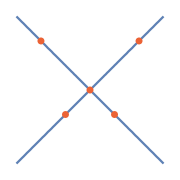
-Graphics-(-1+x-y) (1+x+y)

```mathematica
points={{-2,1},{-1,-2},{1,-2},{2,1},{0,-1}};
conic=FivePointConic[points,{x,y}];
curve=ContourPlot[conic==0,{x,-3,3},{y,-4,4}][[1]];
Labeled[Graphics[{curve,{,Point[points]}}, ImageSize-> Small],conic]
```

See the properties of the non-degenerate conics with the resource function ConicProperties:

```mathematica
base={{-2,1},{-1,-2},{1,-2},{2,1}};
last={{0,0},{0,2},{0,-3},{1,2}};
ResourceFunction["ConicProperties"][FivePointConic[Append[base,#]]==0,{x,y}]&/@last
```

{<|Type→Hyperbola,Equation→2 x^2-5 y-3 y^2==0,Foci→{{0,-5/12 (2+√10)},{0,5/12 (-2+√10)}},Vertices→{{0,-5/3},{0,0}},Eccentricity→√(5/2),Asymptotes→{y==-5/6-√(2/3) x,y==-5/6+√(2/3) x},Center→{0,1/2 (5/12 (-2+√10)-5/12 (2+√10))},SemimajorAxisLength→5/6,SemiminorAxisLength→5/(2 √6),Directrices→{y==1/6 (-5-√10),y==-5/6},AxesOfSymmetry→{x==0,y==-5/6},SemiLatusRectum→5/4,RotationAngle→-π/2,ConjugateHyperbola→6 x^2-15 y-9 y^2==50,BaseConic→<|Equation→(36 x^2)/25-(24 y^2)/25==1,RotationAngle→-π/2,DisplacementFromOrigin→{0,1/2 (5/12 (-2+√10)-5/12 (2+√10))}|>|>,<|Type→Ellipse,Equation→-22+4 x^2+y+5 y^2==0,Foci→{{-21/20,-1/10},{21/20,-1/10}},Vertices→{{-21/(4 √5),-1/10},{21/(4 √5),-1/10}},Covertices→{{0,-11/5},{0,2}},Eccentricity→1/(√5),Center→{0,-1/10},SemimajorAxisLength→21/(4 √5),SemiminorAxisLength→21/10,AreaEnclosed→(441 π)/(40 √5),SemiLatusRectum→21/(5 √5),Directrices→{x==-(441 √5)/188,x==(441 √5)/188},AxesOfSymmetry→{y==-1/10,x==0},Circumference→(21 EllipticE[1/5])/(√5),RotationAngle→0,BaseConic→<|Equation→(80 x^2)/441+(100 y^2)/441==1,RotationAngle→0,DisplacementFromOrigin→{0,-1/10}|>|>,<|Type→Parabola,Equation→-3+x^2-y==0,Focus→{0,-11/4},Vertex→{0,-3},Directrix→y==-13/4,FocalParameter→1/2,SemiAxisLength→1/4,AxisOfSymmetry→x==0,SemiLatusRectum→1/2,RotationAngle→0,BaseConic→<|Equation→x^2==y,RotationAngle→0,DisplacementFromOrigin→{0,-3}|>|>,<|Type→Circle,Equation→-5+x^2+y^2==0,Radius→√5,Circumference→2 √5 π,Center→{0,0},AreaEnclosed→5 π|>}

### Neat Examples

A function for characterizing a conic section:

```mathematica
CharacterizeConic[poly_]:=Module[{A,B,C,D,E,F,discriminant,coeff},
If[Length[FactorList[poly]]>2 || NumericQ[poly],Return["D" (*degenerate*)]];
coeff=Flatten[CoefficientList[poly,{x,y},{3,3}]];
{A,B,C,D,E,F}=coeff[[{7,5,3,4,2,1}]]; 
discriminant = B^2-4A C;
Which[
B==0 &&A==C,"C" (*circle*),
discriminant==0,"P" (*parabola*),
discriminant<0,"E" (*ellipse*),
discriminant>0,"H" (*hyperbola*),
True, "D" (*degenerate*)
]]
```

A sample conic section:

```mathematica
SeedRandom[2];
r5=RandomInteger[{-10,10},{5,2}];
poly=FivePointConic[r5]
```

-29+18 x+11 x^2+207 y+9 x y-24 y^2

The above polynomial defines a hyperbola:

```mathematica
CharacterizeConic[poly]
```

H

Degenerate conics appear frequently when selecting from a limited lattice:

```mathematica
SeedRandom[1];
pols=Table[FivePointConic[RandomInteger[{-4,4},{5,2}]],{5000}];
SortBy[Tally[CharacterizeConic/@pols],-Last[#]&]
```

{{H,2131},{D,1796},{E,1066},{P,4},{C,3}}

For random real-valued points, the result is always a hyperbola or ellipse:

```mathematica
SeedRandom[1];
pols=Table[FivePointConic[RandomReal[{-4,4},{5,2}]],{5000}];
SortBy[Tally[CharacterizeConic/@pols],-Last[#]&]
```

{{H,3555},{E,1445}}

## Source & Additional Information

### Contributed By

Ed Pegg Jr

### Keywords

conic sections

hyperbola

parabola

circle

ellipse

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

Circle

Cone

Circumsphere

### Related Resource Objects

ConicProperties

EllipseProperties

FociPointEllipse

FociPointHyperbola

HyperbolaProperties

ParabolaProperties

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.